```mathematica
f[x_]:=α Cos[√λ x]-α Cot[√λ α] Sin[√λ x]/;x<a
```

```mathematica
f[x_]:=β Sin[√λ a]/Sin[√λ(a-1)] Cos[√λ x]-β Cos[√λ a]/Sin[√λ(a-1)] Sin[√λ x]/;x>=a
```

```mathematica
D[α Cos[√λ x]-α Cot[√λ a] Sin[√λ x],x]
```

-α √λ cot(a √λ) cos(√λ x)-α √λ sin(√λ x)

```mathematica
∫_0^a (D[α Cos[√λ x]-α Cot[√λ a] Sin[√λ x],x]^2-λ (α Cos[√λ x]-α Cot[√λ a] Sin[√λ x])^2)ⅆx
```

α^2 √λ cot(a √λ)

```mathematica
∫_a^1 (D[β Sin[√λ a]/Sin[√λ(a-1)] Cos[√λ x]-β Cos[√λ a]/Sin[√λ(a-1)] Sin[√λ x],x]^2-λ (β Sin[√λ a]/Sin[√λ(a-1)] Cos[√λ x]-β Cos[√λ a]/Sin[√λ(a-1)] Sin[√λ x])^2)ⅆx
```

-β^2 √λ cot((a-1) √λ)

```mathematica
DSolve[{f''[x]==-λ f[x],f[1]==β,f[a]==0},f[x],x]
```

{{f(x)→(β (sin(a √λ) cos(√λ x)-cos(a √λ) sin(√λ x)))/(cos(√λ) sin(a √λ)-sin(√λ) cos(a √λ))}}

```mathematica
β=(f(1))/(f(0)); f(a)=0;
min{∫_0^1 (f')^2-λ f^2 ⅆx}=(f(0))^2(√λ Cot[a √λ]+β^2 √λ Cot[(a-1)√λ])
```

cot((√λ)/3)+4 cot((2 √λ)/3)

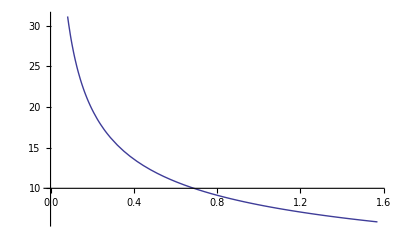

```mathematica
Cot[a √λ]+β^2 Cot[(1-a) √λ]/.{a->1/3,β->2}
Plot[%,{λ,0,π/2}]
```

```mathematica
a=1/2;
Cot[a √λ]+β^2 Cot[(1-a)√λ]
Plot3D[Cot[a √λ]+β^2 Cot[(1-a)√λ],{λ,0,π^2},{β,-5,5},AxesLabel->Automatic,PlotRange->{0,10}]
```

β^2 cot((√λ)/2)+cot((√λ)/2)

-Graphics3D-

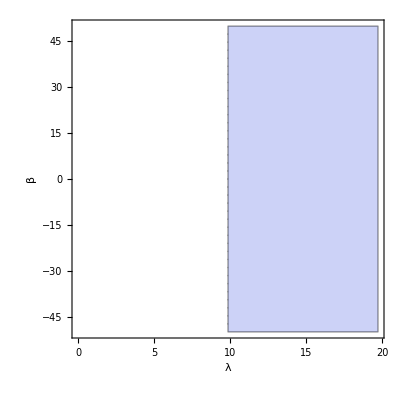

```mathematica
a=9/18;
RegionPlot[Cot[a √λ]+β^2 Cot[(1-a)√λ]≤0,{λ,0,2 π^2},{β,-50,50},AxesLabel->Automatic]
```

```mathematica
Root
```

```mathematica
Clear[a,β,λ]
```

```mathematica
a=1/2;
Cot[a √λ[β]]+β^2 Cot[(1-a)√λ[β]]
Solve[{D[Cot[a √λ[β]]+β^2 Cot[(1-a)√λ[β]],β]==0&&Cot[a √λ[β]]+β^2 Cot[(1-a)√λ[β]]==0},β]
```

β^2 cot((√(λ(β)))/2)+cot((√(λ(β)))/2)

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{-(β^2 λ'(β) csc^2((√(λ(β)))/2))/(4 √(λ(β)))-(λ'(β) csc^2((√(λ(β)))/2))/(4 √(λ(β)))+2 β cot((√(λ(β)))/2)==0∧β^2 cot((√(λ(β)))/2)+cot((√(λ(β)))/2)==0},β]

```mathematica
λ(a)=Piecewise[{{π^2/(4(1-a)^2), 0≤ a<1/2}, {π^2/(4 a^2), 1≥ a≥1/2}}]
```